## ODE Solvers and Interpolating Functions: everything you didn’t think you needed to know and were afraid to ask.

We have seen that Mathematica returns numerical IVP solutions as “Interpolating Functions”. We should know what it is and how to do things with it.  Here is the solution to a simple 1st order IVP.  The numerical solution has some “Methods”.

InterpolatingFunction[…]

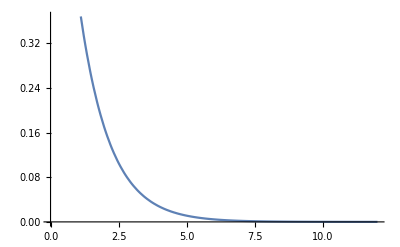

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

```mathematica
ySol=NDSolveValue[{y'[t]==-0.9 y[t],y[0]==1},y,{t,0, 12}]
Plot[ySol[t],{t,0,12}]
ySol["Methods"]
```

The question is what does all this mean?  Well lets see,  we can differentiate the solution of the ODE a bit but not for ever!

```mathematica
TabView[{
"y"->Plot[ySol[t],{t,0, 12}],
"y'"->Plot[ySol'[t],{t,0, 12}],
"y''"->Plot[ySol''[t],{t,0, 12}],
"y'''"->Plot[ySol'''[t],{t,0, 12}],
"y^(4)"->Plot[ySol''''[t],{t,0, 12}]
}]
```

12345

This tells us that the numerical solution is actually just a whole bunch of bits of cubic. On each sub interval the heights and slopes are known at both ends. This is 4 conditions on each subinterval which determines the 4 coefficients in each subinterval cubic "a_3t^3+a_2t^2+a_1t+a_0". This interpolation process is called a Hermite cubic spline!  You can confirm this by asking what the interpolation method is.

```mathematica
ySol["InterpolationMethod"]
```

Hermite

In fact everything you can imagine is available: the input domain, t values used and y values computed are

```mathematica
ySol["Domain"]
ySol["Coordinates"]
ySol["ValuesOnGrid"]
```

{{0.,12.}}

{{0.,0.000224294,0.000448588,0.0054681,0.0104876,0.0155071,0.0313412,0.0471752,0.0630092,0.0788433,0.110511,0.142179,0.173848,0.205516,0.237184,0.334077,0.43097,0.505453,0.579936,0.654418,0.728901,0.803384,0.877867,1.01914,1.16041,1.27501,1.38961,1.50421,1.61881,1.73341,1.84801,1.96261,2.12296,2.28331,2.44366,2.60401,2.76437,2.92472,3.08507,3.27749,3.4699,3.66232,3.85474,4.04716,4.23958,4.43199,4.62441,4.84663,5.06886,5.29108,5.5133,5.73552,5.95774,6.17997,6.40219,6.62441,6.84663,7.06886,7.32744,7.58603,7.84461,8.1032,8.36178,8.62037,8.87895,9.15673,9.43451,9.71229,9.99007,10.2678,10.5456,10.8234,11.1776,11.5318,11.7659,12.}}

{1.,0.999798,0.999596,0.995091,0.990606,0.986141,0.972187,0.958431,0.94487,0.9315,0.905326,0.879887,0.855163,0.831134,0.80778,0.740323,0.678498,0.634507,0.593367,0.554895,0.518917,0.485272,0.453809,0.399627,0.351914,0.317427,0.286319,0.25826,0.232951,0.210122,0.18953,0.170956,0.147982,0.128095,0.110881,0.0959802,0.0830818,0.0719168,0.0622522,0.0523535,0.0440287,0.0370277,0.0311399,0.0261883,0.0220241,0.018522,0.0155768,0.0127532,0.0104415,0.00854875,0.00699913,0.0057304,0.00469165,0.0038412,0.00314491,0.00257483,0.0021081,0.00172596,0.0013676,0.00108365,0.000858648,0.000680367,0.000539102,0.000427168,0.000338475,0.000263604,0.000205295,0.000159884,0.000124518,0.0000969745,0.0000755238,0.0000588179,0.0000427617,0.0000310894,0.0000251836,0.0000203996}

If we just want the last time or the last point we can have them

```mathematica
ySol["Coordinates"]⟦1,-1⟧
ySol["ValuesOnGrid"]⟦-1⟧
```

12.

0.0000203996

So the following sets up a parameterized system of ODEs which stops when it hits "y_1 = 0" then plots a whole bunch of those solutions with different starting points.  We need the tEnd line because each curve ends at a different time.

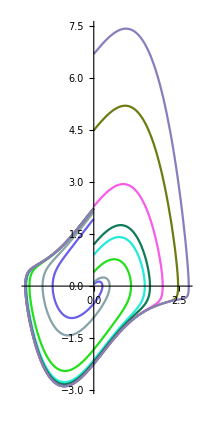

```mathematica
Clear[μ,x,f]
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
μ=1.2;
TMax=12;
ySol=ParametricNDSolveValue[{y'[t]==f[μ][y[t]],y[0]=={0,x}},y,{t, 0,TMax},x,
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1}];
xVals={0.05,.1,0.4,0.9,1.2,2.3,4.5,6.7};
Show[Table[
p=ySol[x];
tEnd=p["Domain"][[1,2]];
ParametricPlot[p[t],{t,0,tEnd},PlotStyle->RandomColor[]],
{x,xVals}],PlotRange->All]
```

## Visualizing Functions

### One input one output: x_1→f(x_1) i.e f:ℝ→ℝ

There are lots of ways to plot a calculus one function with one input and one output

```mathematica
f[x1_]:= x1 +Sin[x1^2]
TabView[{
"Plot"->Plot[f[x1],{x1,-2,2}],
"ParPlot"->ParametricPlot[{x1,f[x1]},{x1,-2,2},Frame->True,GridLines->Automatic],
"InvParPlot"->ParametricPlot[{f[x1],x1},{x1,-2,2},Frame->True,GridLines->Automatic],
"ParPlotColor x"->ParametricPlot[{x1,f[x1]},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x,f},Hue[x]]],
"ParPlotColor f"->ParametricPlot[{x1,f[x1]},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x,f},Hue[f]]],
"Flat"->ParametricPlot[{x1,0},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[x,Hue[f[x]]]]
},2]
```

123456

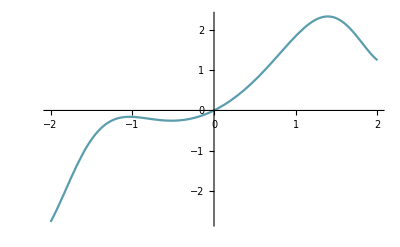

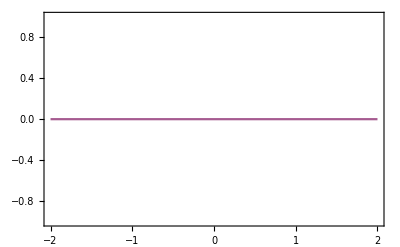

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### One input two outputs: x_1→{f1(x_1),f2(x_1)} i.e f:ℝ→ℝ^2

There are lots of ways to plot a calculus two function with one input and two outputs

```mathematica
f[x1_]:= {x1 +Sin[x1^2],Cos[x1]+x1}
TabView[{
"ParPlot"->ParametricPlot[f[x1],{x1,-2,2},Frame->True,GridLines->Automatic],
"Plot"->Plot[f[x1],{x1,-2,2},Frame->True,GridLines->Automatic],
"ParPlotColor 1"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[x1]]],
"ParPlotColor 2"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[f1]]],
"ParPlotColor 3"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[f2]]]
},1]
```

12345

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### One input three outputs: x_1→{f1(x_1),f2(x_1),f3(x1)} i.e f:ℝ→ℝ^3

There are lots of ways to plot a calculus three function with one input and three outputs

```mathematica
f[x1_]:= {x1 +Sin[x1^2],Cos[x1]+x1,-x1^2+ArcTan[Cos[1+x1^2]]}
TabView[{
"ParPlot3D"->ParametricPlot3D[f[x1],{x1,-2,2},FaceGrids->All],
"Plot"->Plot[f[x1],{x1,-2,2}],
"ParPlot3DColor 1"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[x1]]],
"ParPlot3DColor 2"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f1]]],
"ParPlot3DColor 3"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f2]]],
"ParPlot3DColor 4"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f3]]],
"ParPlot Color f3"->ParametricPlot[f[x1][[1;;2]],{x1,-2,2},
PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1},Hue[f[x1][[3]]]]]
},1]
```

1234567

```mathematica
123456
```

```mathematica
12345
```

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### Two input one outputs: {x_1,x_2}→f1(x_1,x_2) i.e f:ℝ^2→ℝ

There are lots of ways to plot a calculus three function with one input and three outputs

```mathematica
f[{x1_,x2_}]:= -x1^2+x2*ArcTan[Cos[1+x1^2+x2^2]]
TabView[{
"Plot3D"->Plot3D[f[{x1,x2}],{x1,-2,2},{x2,-2,2},FaceGrids->All],
"Plot3D Hue"->Plot3D[f[{x1,x2}],{x1,-2,2},{x2,-2,2},FaceGrids->All,ColorFunction->Function[{x1,x2,f},Hue[f]]],
"ContourPlot Hue"->ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},ColorFunction->Hue,Contours->20],
"ContourPlot Default"->ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},Contours->20]
},2]
```

1234

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### Two input two outputs: {x_1,x_2}→{f1(x_1,x_2),f2(x_1,x_2)} i.e f:ℝ^2→ℝ^2

There are a couple of ways to plot a calculus three function with two input and two outputs

```mathematica
f[{x1_,x2_}]:= {3+3x1+0.2*Sin[x2 x2],1+0.5x2-0.1 x1^2+0.2x2*ArcTan[x1+x2]}
p[r_,θ_]:=r{Cos[θ],Sin[θ]}
SqPic=ParametricPlot[{{x1,x2},f[{x1,x2}]},{x1,-2,2},{x2,-2,2},Mesh->Automatic,
MeshStyle->{Red, Blue}];
CirclePic=ParametricPlot[{p[r,θ],f[p[r,θ]]},{θ,0,2π},{r,0,2},Mesh->Automatic,MeshStyle->{Cyan, Black}];
TabView[{
"ParametricPlot Square"->SqPic,
"ParametricPlot Circle"->CirclePic,
"Together"->Show[CirclePic,SqPic]
},1]
```

123

### Three input three outputs: {x_1,x_2,x_3}→{f1(x_1,x_2,x_3),f2(x_1,x_2,x_3),f3(x_1,x_2,x_3)} i.e f:ℝ^3→ℝ^3

There are a couple of ways to plot a calculus three function with three input and three outputs

```mathematica
A=({{1.2, 3, 1}, {4.3, 2.4, -2}, {-3, 2, 4.5}});
SingularValueList[A]
p[r_,θ_,ϕ_]:=r{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
r=0.5;
ParametricPlot3D[{p[r,θ,ϕ],A.p[r,θ,ϕ]},{θ,0,2π},{ϕ,0,π},Mesh->Automatic,MeshStyle->{Red, Blue},PlotPoints->123,PlotRange->All]
```

{6.9359,4.97975,0.187903}

-Graphics3D-

# First Return y'=f(y) e.g. y_1==0

The VDP system and the Rosseler system both cross y_1==0 repeatedly.  The first return map (fory_1==0) is a natural way to look at the behavior of the system as a map from the plane y_1=0 onto the plane y_1=0.

We are going to look at this first for the 2D VDP problem and then see how much messier it gets for the 3D Roseller system.

First Return Map (Informal Definition)
The first return map for an ODE y'=f(y) on a surface 𝒮  is where the solution of the  ODE first returns to the surface 𝒮   (in the same direction) as a function on 𝒮.

## Intro First Return Map for VDP System y_1==0

Our VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
I am going to look at initial conditions y_0=(0,x) and catch the output y_*=(0,r(x)) the first time it crosses y_1==0 heading in the same direction. In Mathematica there is a way to catch values from the ODE solver when it locates an event.

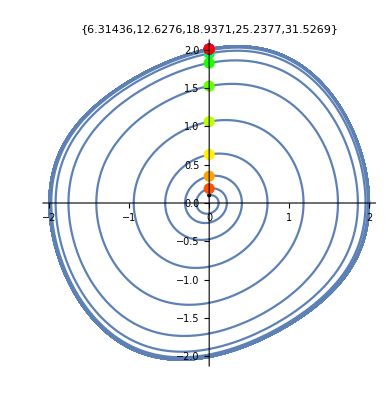

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=124.5;y0={0,0.1};μ=0.2; ϵ=1;
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0,
J'[t]==Df[μ][y[t]].J[t],J[0]=={{1,0},{0,1}}
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
ParametricPlot[ySol[t],{t,0, TMax},
Epilog->{{Black,Point[ySol[0]]},Table[{Hue[i/Length[Data]],PointSize[0.02],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
PlotLabel->Data⟦1;;5,1⟧]
```

## Intro First Return Map for Rosseller System y_1==0

The same trick for the  Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=54;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
BasePic=Show[
ParametricPlot3D[ySol[t],{t,0, TMax},
PlotRange->All],
Graphics3D[{Black,PointSize[0.02],Point[ySol[0]]}],
Graphics3D[{Opacity[0.5],Yellow,Polygon[15{{0,-1,0},{0,1,0},{0,1,2},{0,-1,2}}]}]];
Dots=Graphics3D[{PointSize[0.02],Table[{Hue[i/Length[Data]],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
Axes->True,BoxRatios->{1, 1, 1}];
TabView[{
"y"->BasePic,
"y+"->Show[BasePic,Dots,PlotLabel->Data⟦All,1⟧],
"Dots"->Dots
}]
```

123

## Pic: First Return Map for VDP System y_1==0

Our VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
I am going to look at initial conditions y_0=(0,x) and catch the output y_*=(0,r(x)) the first time it crosses y_1==0 heading in the same direction. In Mathematica there is a way to catch stop the ODE solver at an “event”. In Mathematica there is also a way to easily put parameters into ODE solvers. It looks like this.

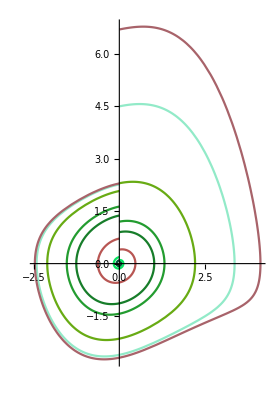

```mathematica
Clear[μ,x,f,Df]
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
μ=0.2;
TMax=12;
ySol=ParametricNDSolveValue[{y'[t]==f[μ][y[t]],y[0]=={0,x}},y,{t, 0,TMax},x,
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1}];
xVals={0.05,.1,0.4,0.9,1.2,2.3,4.5,6.7};
Show[Table[
p=ySol[x];
tEnd=p["Domain"][[1,2]];
ParametricPlot[p[t],{t,0,tEnd},PlotStyle->RandomColor[]],
{x,xVals}],PlotRange->All]
```

All we really want out of this is the last computed y value.

ParametricFunction[<>]

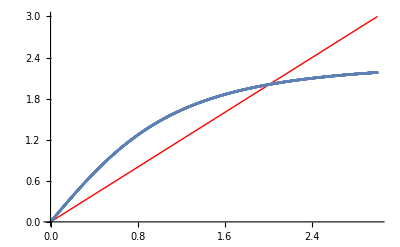

```mathematica
Clear[x,y,t]
ySol=ParametricNDSolveValue[{y'[t]==f[μ][y[t]],y[0]=={0,x}},y,{t, 0,TMax},x,
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1}]
{xMin,xMax,Δx}={0.001,3,0.001};
OutputVals=Table[ySol[x]["ValuesOnGrid"]⟦-1⟧,{x, xMin,xMax,Δx}];
ListPlot[ OutputVals⟦All,2⟧,PlotRange->{{0,xMax},{0,xMax}},DataRange->{xMin,xMax},Prolog->{Red,Line[{{0,0},{xMax,xMax}}]}]
```

This is a pretty boring curve!  What it tells you is that all curves squish into the curve that starts at the crossing point.  The convergence is monotone: if we start below the crossing point we head up; if we start below we head down. It does not jump around at all

## Pic: First Return Map for Rosseller System y_1==0

I am going to

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

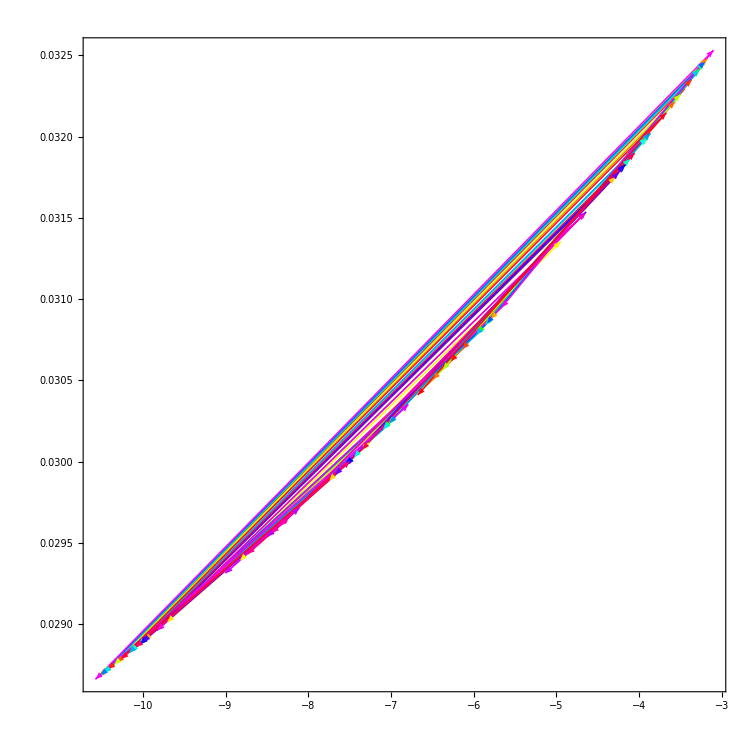

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=540;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
yVals=Data[[All,2,2;;3]];
Graphics[PVals=Table[ 
{Hue[i/Length[yVals]],Arrow[{yVals[[i]], yVals[[i+1]]}]},{i, 1, Length[yVals]-1}],
AspectRatio->1,
Frame->True]
```